```mathematica
Quit
```

```mathematica
Needs["CompiledFunctionTools`"] ;(*use CompilePrint[] to check the compiled code of functions and find "MainEvaluate"*)

(*adjust here the main directory for the project.*)
(* LEX data files should be located in the subdirectory \Lexdata. Census gazetteer files should be located in the subdirectory \2019_Gaz_counties_national. *)
(* MZ correspondences are saved in the subfolder \MobilityZonesV1.1 . Graphs are saved in the subfolder \Graphs.*)
```

```mathematica
SetDirectory["E:\\Dropbox\\mobilityZones\\"];
```

## Setup

## Building Pre-Covid Data

```mathematica
curGwithNames=Import["Lexdata\\county_lex_2020-01-20.csv"];
curG=curGwithNames⟦2;;,2;;⟧;
countyCodes=curGwithNames⟦1,2;;⟧;
ncounties=Length[countyCodes];

Print[DateString[]];
days=20; (*21 days of data from 1/20 (monday, included) end on the Sunday 3 weeks after, 2/9; the loop is over the 20 remaining days *)
Do[
Block[{curDate,curCountyLex,y,m,d,gNames,g},
curDate=DatePlus[{2020,1,20},i];
y=TextString[curDate⟦1⟧];
m="0"<>TextString[curDate⟦2⟧];
d=If[curDate⟦3⟧<10,"0"<>TextString[curDate⟦3⟧],TextString[curDate⟦3⟧]];
curCountyLex="Lexdata\\county_lex_"<>y<>"-"<>m<>"-"<>d<>".csv";
(*Print[curCountyLex];*)
gNames=Import[curCountyLex];
g=gNames⟦2;;,2;;⟧;
curG=curG+g;
],{i,1,days}
];
Print[DateString[]];

(*all bilateral data*)
preCovid=curG/(days+1);
```

## Importing other codes and county population and land area data

Codes

```mathematica
(*--- which state code is in each row of the LEX data? used in routines below*)
stateCodes=IntegerPart[countyCodes/1000.];

(*--- list of county codes and abbreviations to iterate over*)
stateCodesList={1,2,4,5,6,8,9,10,12,13,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,49,50,51,53,54,55,56};
stateAbbrList={"AL","AK","AZ","AR","CA","CO","CT","DE","FL","GA","HI","ID","IL","IN","IA","KS","KY","LA","ME","MD","MA","MI","MN","MS","MO","MT","NE","NV","NH","NJ","NM","NY","NC","ND","OH","OK","OR","PA","RI","SC","SD","TN","TX","UT","VT","VA","WA","WV","WI","WY"};
```

Importing population in 2019 and land area of counties in the LEX data

```mathematica
allPopwithNames=Import["co-est2019-onlypop.csv"];
(*allPopwithNames⟦1⟧*)

pop2019={};
censusGazwithNames=Import["2019_Gaz_counties_national\\2019_Gaz_counties_national.txt","tsv"];
censusGazwithNames⟦1⟧
countyArea={};

Do[
Block[{ind},

ind=Flatten[Position[allPopwithNames⟦All,3⟧,countyCodes⟦curPos⟧ ]];
pop2019=Join[pop2019,allPopwithNames⟦ind,6⟧];

ind=Flatten[Position[censusGazwithNames⟦All,2⟧,countyCodes⟦curPos⟧]];
countyArea=Join[countyArea,censusGazwithNames⟦ind,7⟧];
],

{curPos,1,Length[countyCodes]}
];
```

{USPS,GEOID,ANSICODE,NAME,ALAND,AWATER,ALAND_SQMI,AWATER_SQMI,INTPTLAT,INTPTLONG}

## Loading daily data in a vector

```mathematica
Print[DateString[]];
dailydata={};
days=107; (* days of data from 1/20 (monday) to 5/5 *)
Do[
Block[{curDate,curCountyLex,y,m,d,gNames,g},
curDate=DatePlus[{2020,1,19},i];
y=TextString[curDate⟦1⟧];
m="0"<>TextString[curDate⟦2⟧];
d=If[curDate⟦3⟧<10,"0"<>TextString[curDate⟦3⟧],TextString[curDate⟦3⟧]];
curCountyLex="Lexdata\\county_lex_"<>y<>"-"<>m<>"-"<>d<>".csv";
Print[curCountyLex];
gNames=Import[curCountyLex];
g=gNames⟦2;;,2;;⟧;
dailydata=Join[dailydata,{g}];
],{i,1,days}
];
Print[DateString[]];
```

Thu 14 May 2020 07:31:31

Lexdata\county_lex_2020-05-05.csv

Thu 14 May 2020 07:38:15

```mathematica
Dimensions[dailydata]
```

{107,2018,2018}

## Functions

## Mobility components

The compiled function adjmC generates a symmetric matrix of links.

```mathematica
adjmC=Compile[{{mm,_Real,2},{thr,_Real,0},{ll,_Real,0}},
Module[{dirG,dirGt,adjmOut},
dirG=Table[If[mm⟦i,j⟧≥thr,1,0],{i,1,ll},{j,1,ll}];
dirGt=Transpose[dirG];
adjmOut=(dirG+dirGt)-dirG dirGt;
adjmOut
]];
```

The function mobilityComponents takes:
1) a bilateral county dataset (data)
2) associated county codes (couCodes)
3) range of mobility thresholds t (range), 
and returns, for each threshold:
1) a graph object derived from adjacency matrices (adjOutTemp);
2) an array of county sequence indices (the position of the county in the LEX data) with the list of components of the graph (mzTemp); each element in the array contains one connected component for the given threshold
3) the same information in 2), with county FIPS codes (mzCodesTemp).
These elements are all collected in three separate arrays, adjOut, mzOut, mzCodesOut.

```mathematica
mobilityComponents[data_,couCodes_,range_]:=Module[{adjOut,mzOut,mzCodesOut,nc},
adjOut={};
mzOut={};
mzCodesOut={};
nc=Dimensions[data]⟦1⟧;
Do[ (*for each threshold t*)
Block[{dirG,dirGt,adjm,adjTemp,mzTemp,mzCodesTemp,mmIn},

mmIn=data;
adjm=adjmC[mmIn,threshold,nc];

adjTemp=AdjacencyGraph[adjm];
adjOut=Join[adjOut,adjTemp];

mzTemp=ConnectedComponents[adjTemp];
mzOut=Join[mzOut,{mzTemp}];

mzCodesTemp=Table[couCodes⟦mzTemp⟦i⟧⟧,{i,1,Length[mzTemp]}];
mzCodesOut=Join[mzCodesOut,{mzCodesTemp}];

],{threshold,range⟦1⟧,range⟦2⟧,range⟦3⟧}];

{adjOut,mzOut,mzCodesOut}

];
```

## Creating codes

A simple function to add zeros before a numerical code, and transform it into a string. ndigits=3 for the threshold code, and ndigit=4 for the progressive MZ code.

```mathematica
strFill[code_,ndigits_]:=Module[{codeOut,d1,d2,d3},

If[ndigits==3,
d1="00";
d2="0";
d3=""];
If[ndigits==4,
d1="000";
d2="00";
d3="0"];

If[code<10,codeOut=d1<>ToString[IntegerPart[code]]];
If[code≥ 10 && code≤99,codeOut=d2<>ToString[IntegerPart[code]]];
If[code≥ 100&& code≤999,codeOut=d3<>ToString[IntegerPart[code]]];
If[code≥ 1000,codeOut=ToString[IntegerPart[code]]];

codeOut

];
```

The function assignCode takes a partition (curMz) with county indices (all the components of the mobility graph for a given threshold) and assigns MZ codes to each partition.
The code is a combination of a geographical identifier (geo) a threshold in percentage terms (thresholdValue) and a progressive MZ identifier built in the routine. 
The progressive identifier is sorted so that Mobility Zones that contain counties with lower FIPS codes are assigned a value earlier.

```mathematica
assignCode[curMz_,geo_,thresholdValue_]:=Module[{curId,c,emptyGroups,mbClassTemp,x,nc,geocode,thresholdString},

x=curMz;
nc=Length[Flatten[x]];

(*Print["dimensions ",Dimensions[curMz]];*)
(*initializing id*)
curId=0;
(*initializing county counter*)
c=1;
(*exit flag*)
emptyGroups=0;


(*list that will contain the mobility zone ids for the current partition*)
mbClassTemp=Table[-1,{i,1,nc}];

While[c≤2018 && emptyGroups==0,

Block[{finding},

(*Print["current county counter: ",c];*)

(*looking for the next county counter; if found, then the length of "finding" is positive.*)
finding=Position[x,c];

If[Length[finding]>0,
(*In this case,  assign to all the counties in the same group of c the next curId code in mbClassTemp*)

Block[{sizeMb,curEl},

(*next id available*)
curId=curId+1;

(*Current element number in the partition examined, and the number of counties in it*)
curEl=Flatten[finding]⟦1⟧;

sizeMb=Length[x⟦curEl⟧];

(*setting the new id on the corresponding counties*)
mbClassTemp⟦ x⟦curEl⟧ ⟧=Table[curId,{i,1,sizeMb}];

(*dropping the counties from the current zone set*)
x=Drop[x,{curEl}];

(*Print[x];*)

];

];

(*next county counter*)
c++;
(*checking if done before exhausting all the counties*)
If[Length[x]==0,emptyGroups=1];

];

];

geocode=Table[geo<>strFill[thresholdValue,3]<>"."<>strFill[mbClassTemp⟦i⟧,4],{i,1,nc}];
Join[{geo<>strFill[thresholdValue,3]},geocode]

];
```

## Creating Partitions

## United States: all mobility zones

```mathematica
(*list of threshold of interaction t*)
thresholdList={0,1,0.05};
(*labels for MZ codes: threshold times 100*)
series=Table[100 i, {i,thresholdList⟦1⟧,thresholdList⟦2⟧,thresholdList⟦3⟧}];
(*computing partitions for California*)
{adj,mz,mzCodes}=mobilityComponents[preCovid,countyCodes,thresholdList];
(*assigning codes*)
out1=Table[assignCode[mz⟦i⟧,"US",series⟦i⟧],{i,1,Length[mz]}];
(*labels*)
firstcol=Join[{"county"},countyCodes];
(*output*)
out2=Transpose[Join[{firstcol},out1]];
Export["MobilityZonesV1.1\\MobilityZonesUS.csv",out2];
```

## United States: mobility zones over time

### Generating MZs for each day

```mathematica
adjTime={};
mzTime={};
mzCodesTime={};
mzPop={};
mzArea={};
(*list of threshold of interaction t*)
thresholdList={0,1,0.05};
Do[
Block[{gtemp,adjTemp,mzTemp,mzCodesTemp,num},
gtemp=dailydata⟦i⟧(*Total[ dailydata⟦i;;i+6⟧ ]/7*);
{adjTemp,mzTemp,mzCodesTemp}=mobilityComponents[gtemp,countyCodes,thresholdList];
(*Print[Dimensions[mzTemp]];*)
mzTime=Join[mzTime,{mzTemp}];
(*Print[Dimensions[mzTime]];*)
mzCodesTime=Join[mzCodesTime,{mzCodesTemp}];

num=Table[Table[Total[pop2019⟦ mzTemp⟦j,i⟧ ⟧],{i,1,Length[mzTemp⟦j⟧]}],{j,1,Length[series]}];
mzPop=Join[mzPop,{num}];

num=Table[Table[Total[countyArea⟦ mzTemp⟦j,i⟧ ⟧],{i,1,Length[mzTemp⟦j⟧]}],{j,1,Length[series]}];
mzArea=Join[mzArea,{num}];


Print[i," - ",DateString[]];

],
{i,1,107}];

mzNumberTime={};
Do[Block[{num},
num=Table[Length[mzTime⟦i,threshold⟧],{i,1,107}];
mzNumberTime=Join[mzNumberTime,{num}];

],
{threshold,1,Length[series]}];
```

1 - Thu 14 May 2020 07:52:02

107 - Thu 14 May 2020 10:32:06

### Producing graphs

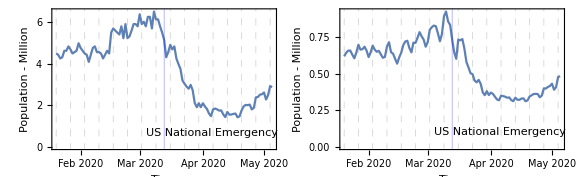

graphs\MZovertime.pdf

```mathematica
totdays=107;
gridDates=Join[Table[{DatePlus[{2020,1,20},i],Dashed},{i,0,totdays,7}],
{{{2020,3,13},Blue}}];


yaxis=Table[1. Mean[mzPop[[day,5]]]/10^6,{day,1,totdays}];
g1=DateListPlot[yaxis,{{2020,1,20},DatePlus[{2020,1,20},totdays-1],"Day"},
DateTicksFormat->{"MonthShort","/","Day"},Frame->{{True,False},{True,False}},

FrameLabel->{"Time","Population - Million"},GridLines->{gridDates,None},PlotLabels->Placed["US National Emergency",{{2020,4,11},1}]];



yaxis=Table[1. Mean[mzPop[[day,8]]]/10^6,{day,1,totdays}];
g2=DateListPlot[yaxis,{{2020,1,20},DatePlus[{2020,1,20},totdays-1],"Day"},
DateTicksFormat->{"MonthShort","/","Day"},Frame->{{True,False},{True,False}},
FrameLabel->{"Time","Population - Million"},GridLines->{gridDates,None},PlotLabels->Placed["US National Emergency",{{2020,4,11},0.15}]];


gOut=GraphicsGrid[{{g1,g2}},ImageSize->Large,Spacings->{0,0}]
Export["graphs\\MZovertime.pdf",gOut]
```

## Loop for all U.S. states

```mathematica
(*threshold of interactions and labels for MZ codes: threshold times 100*)
thresholdList={0,1,0.05};
series=Table[100 i, {i,thresholdList⟦1⟧,thresholdList⟦2⟧,thresholdList⟦3⟧}];

Do[

Block[{statePositions,g1State,countyCodesState,adj,mz,mzCodes,out1,firstcol,out2},

(*position of counties of the current US state in the main data*)
statePositions=Flatten[Position[stateCodes,stateCodesList⟦curState⟧ ]];

(*submatrix of the preCovid matrix that contains flows between counties in this state*)
g1State=preCovid⟦statePositions,statePositions⟧;

(*subvector of the countyCode names that contains the codes of the current county*)
countyCodesState=countyCodes⟦statePositions⟧;

(*computing partitions for the current state*)
{adj,mz,mzCodes}=mobilityComponents[g1State,countyCodesState,thresholdList];


(*assigning codes to MZs for the current state*)
out1=Table[assignCode[mz⟦i⟧,stateAbbrList⟦curState⟧,series⟦i⟧],{i,1,Length[mz]}];

(*labels*)
firstcol=Join[{"county"},countyCodesState];

(*output*)
out2=Transpose[Join[{firstcol},out1]];



Export["MobilityZonesV1.1\\MobilityZones"<>stateAbbrList⟦curState⟧<>".csv",out2];

],
{curState,1,50}
]
```

## California: mobility zones over time

### Generating MZs for each day

```mathematica
adjTimeCA={};
mzTimeCA={};
mzCodesTimeCA={};
mzPopCA={};
mzAreaCA={};

(*position of counties of the California in the main data*)
statePositions=Flatten[Position[stateCodes,6]];
(*subvector of the countyCode names that contains the codes of the current county; same for  population and area*)
countyCodesState=countyCodes⟦statePositions⟧;
statePop=pop2019⟦statePositions⟧;
stateArea=countyArea⟦statePositions⟧;

Do[
Block[{gtemp,adjTemp,mzTemp,mzCodesTemp,num},


gtemp=dailydata⟦i,statePositions,statePositions⟧;
{adjTemp,mzTemp,mzCodesTemp}=mobilityComponents[gtemp,countyCodesState,thresholdList];

(*Print[Dimensions[mzTemp]];*)
mzTimeCA=Join[mzTimeCA,{mzTemp}];

(*Print[Dimensions[mzTime]];*)
mzCodesTimeCA=Join[mzCodesTimeCA,{mzCodesTemp}];

num=Table[Table[Total[statePop⟦ mzTemp⟦j,i⟧ ⟧],{i,1,Length[mzTemp⟦j⟧]}],{j,1,Length[series]}];
mzPopCA=Join[mzPopCA,{num}];

num=Table[Table[Total[stateArea⟦ mzTemp⟦j,i⟧ ⟧],{i,1,Length[mzTemp⟦j⟧]}],{j,1,Length[series]}];
mzAreaCA=Join[mzAreaCA,{num}];


(*Print[i," - ",DateString[]];*)

],
{i,1,107}];

mzNumberTimeCA={};
Do[Block[{num},
num=Table[Length[mzTimeCA⟦i,threshold⟧],{i,1,107}];
mzNumberTimeCA=Join[mzNumberTimeCA,{num}];

],
{threshold,1,Length[series]}];
```

### Producing graphs

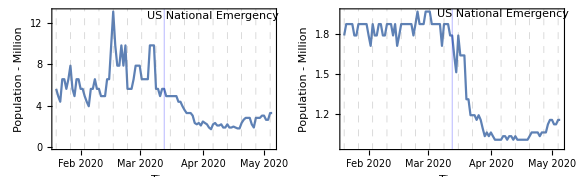

graphs\MZCAovertime.pdf

```mathematica
totdays=107;
gridDates=Join[Table[{DatePlus[{2020,1,20},i],Dashed},{i,0,totdays,7}],
{{{2020,3,13},Blue}}];


yaxis=Table[1. Mean[mzPopCA[[day,5]]]/10^6,{day,1,totdays}];
g1=DateListPlot[yaxis,{{2020,1,20},DatePlus[{2020,1,20},totdays-1],"Day"},
DateTicksFormat->{"MonthShort","/","Day"},Frame->{{True,False},{True,False}},

FrameLabel->{"Time","Population - Million"},GridLines->{gridDates,None},PlotLabels->Placed["US National Emergency",{{2020,4,5},12}]];


yaxis=Table[1. Mean[mzPopCA[[day,8]]]/10^6,{day,1,totdays}];
g2=DateListPlot[yaxis,{{2020,1,20},DatePlus[{2020,1,20},totdays-1],"Day"},
DateTicksFormat->{"MonthShort","/","Day"},Frame->{{True,False},{True,False}},
FrameLabel->{"Time","Population - Million"},GridLines->{gridDates,None},PlotLabels->Placed["US National Emergency",{{2020,4,5},1.9}]];
gOut=GraphicsGrid[{{g1,g2}},ImageSize->Large,Spacings->{0,0}]
Export["graphs\\MZCAovertime.pdf",gOut]
```

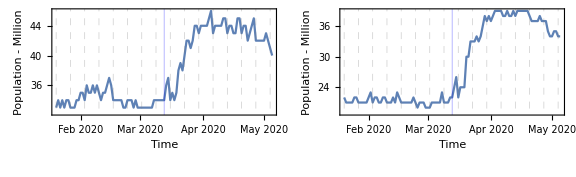

```mathematica
totdays=107;
gridDates=Join[Table[{DatePlus[{2020,1,20},i],Dashed},{i,0,totdays,7}],
{{{2020,3,13},Blue}}];


yaxis=Table[1.mzNumberTimeCA[[10,day]],{day,1,totdays}];
g1=DateListPlot[yaxis,{{2020,1,20},DatePlus[{2020,1,20},totdays-1],"Day"},
DateTicksFormat->{"MonthShort","/","Day"},Frame->{{True,False},{True,False}},

FrameLabel->{"Time","Population - Million"},GridLines->{gridDates,None},PlotLabels->Placed["US National Emergency",{{2020,4,5},1.3}]];


yaxis=Table[1.mzNumberTimeCA[[8,day]],{day,1,totdays}];
g2=DateListPlot[yaxis,{{2020,1,20},DatePlus[{2020,1,20},totdays-1],"Day"},
DateTicksFormat->{"MonthShort","/","Day"},Frame->{{True,False},{True,False}},
FrameLabel->{"Time","Population - Million"},GridLines->{gridDates,None},PlotLabels->Placed["US National Emergency",{{2020,4,5},0.20}]];
gOut=GraphicsGrid[{{g1,g2}},ImageSize->Large,Spacings->{0,0}]
```

## California, number of MZs as a function of threshold

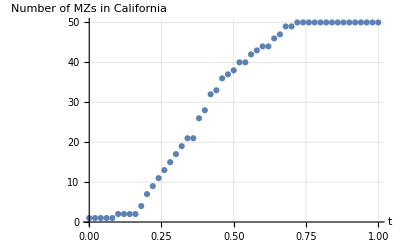

```mathematica
(*position of counties in california*)
statePositions=Flatten[Position[stateCodes,6]];
(*section of the g1 matrix that contains flows between california counties*)
g1State=preCovid⟦statePositions,statePositions⟧;
(*section of the countyCode names that contains the california codes*)
countyCodesState=countyCodes⟦statePositions⟧;

thresholdList={0.0,1,0.02};{adj,mz,mzCodes}=mobilityComponents[g1State,countyCodesState,thresholdList];numberCA=Table[ Length[mz⟦i⟧],{i,1,Length[mzCodes]}];
x=Table[i,{i,thresholdList⟦1⟧,thresholdList⟦2⟧,thresholdList⟦3⟧}];
y=numberCA⟦1;;Length[Table[i,{i,thresholdList⟦1⟧,thresholdList⟦2⟧,thresholdList⟦3⟧} ]]⟧;
z=ListPlot[Transpose[{x,y}],
GridLines->{Automatic},
AxesLabel->{Style["t",Black,Italic,12],Style["Number of MZs in California",Black,Italic,12]}]
Export["graphs\\CAmzNumber.pdf",z];
```